# Coordinatization Tutorial

Graph coordinatization means assigning labels—typically numbers—to vertices so that relations among the labels mirror relations among the corresponding vertices with respect to the underlying graph and some auxiliary structure. A naive approach is to choose a basepoint and use paths from it as labels, but such labels carry no useful structure. In practice, we use numeric coordinates that support algebra and design the coordinatization so that geometric relations become algebraic ones, allowing geometric problems to be solved numerically. This is the role of the Cartesian frame in the Euclidean plane, which turn primitive‑based Euclidean geometry into analytic and algebraic geometry. For graphs, different structures and coordinatization schemes are conceivable, and they need not be numerical. The goal of this tutorial is to explore these ideas, starting from naive implementations of familiar constructions.

#### Classical coordinatizations

This paclet implements the following numerical coordinatization schemes for graphs:

Radar coordinates — distances from selected points.

Orthogonal coordinates — shortest‑path distances from selected lines.

Rectilinear coordinates — coordinates defined via parallelism.

Radar coordinates are simple and robust, but they may collapse distant vertices or separate nearby ones.  They do not seem to preserve any geometric properties of the graph but serve merely as a mean of “triangulating” a point.

Orthogonal coordinates can be used to pullback the Euclidean structure from labels to graph vertices. We can attempt to define the Euclidean structure on the graph by defining the affine structure using the notion of parallels and path-length and the inner product using the shortest path distance and the infra angle. This can be then compared with the pulled back Euclidean structure. Note that in contrast to the plane, graphs are generally anisotropic, so one expects point dependence, except possibly for some isotropic graphs. Orthogonal coordinates preserve the distances to axes by definition, which is part of the inner product.

Rectilinear coordinates preserve parallelism by construction, which is part of the affine structure.

#### Note: Assigning Riemannian geometry to a graph

A mathematically straightforward approach is to consider an r-isometric embedding (preserving mutual distances of all points with distance less than r) of the graph into a Euclidean space and then apply manifold‑learning or data‑analysis methods to identify Riemannian manifolds whose discretizations could correspond to the resulting point cloud, possibly under suitable assumptions on how the points are sprinkled, and suitable assumptions on the scale. For r=1 this reduces to an embedding that preserves edge lengths (e.g. SpringEmbedding in Wolfram), while for r=diam(G) one obtains a fully isometric embedding that intertwines the graph distance to the Euclidean distance. In the former case with edge length 1, the minimal dimension such embedding may exist is given by the size of the largest clique minus 1.  In the latter case the underlying manifold must lie in an affine subspace, typically 1-dimensional, since the graph metric is geodesic and the only curves realizing Euclidean distances are straight lines. Neither the embedding nor the inferred Riemannian manifold is unique, so one naturally obtains an entire moduli space of admissible geometries. Note that the Nash embedding theorem guarantees that any Riemannian manifold can be realized as a submanifold of the Euclidean space, so we do not miss anything. Note that an optimal statement would be that sampling a sufficiently graph at a sufficiently large scale determines almost surely a unique quasi-isomorphism class of Riemannian manifolds, or in the case of hypergraph rewriting, that there is a unique Gromov-Hausdorff limit.

## Setup

The coordinates live in InfraGeometry; the radar map RadarCoordinates lives in the sibling DiscreteGeometry paclet, which InfraGeometry extends with the vertex and vertex-list overloads used below.

```mathematica
Needs["WolframInstitute`InfraGeometry`"];
Needs["WolframInstitute`DiscreteGeometry`"];
```

## Radar coordinates

The radar coordinates of any vertex is the list of its distances to a set reference vertices. A spanning set is a tuple of reference vertices whose radar coordinates distinguish every vertex in the graph; that is, the induced chart is injective. A radar basis is a spanning set such that there exists no strictly smaller spanning set. In contrast to the linear case, not every spanning set contains a basis.

Find a radar basis for a discretized square graph:

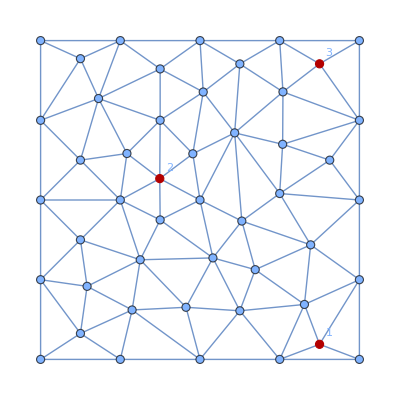

```mathematica
g= MeshConnectivityGraph[ DiscretizeRegion[Rectangle[], MaxCellMeasure->.02, PrecisionGoal->Infinity] ];
b = First @ FindInfraRadarBasis[g];
HighlightGraph[g,MapIndexed[Labeled[#1,#2[[1]]]&,b]]
```

Find how many radar bases exist among all minimal tuples:

```mathematica
bb=GroupBy[Subsets[VertexList[g],{Length @ b}],InfraRadarBasisQ[g,#]&];
Length /@ bb
```

<|False→17284,True→12|>

Select bases with vertices closest and furthest to each other:

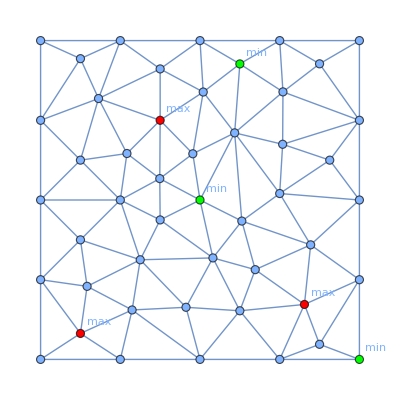

```mathematica
bbSorted= SortBy[bb[True],Total[GraphDistance[g,##]&@@@Subsets[#,{2}]]&];
{bmin, bmax}=TakeList[bbSorted,{1,-1}];
HighlightGraph[g,{Labeled[Style[#,Green],"min"]&@@ bmin,Labeled[Style[#,Red],"max"]&@@ bmax}]
```

Find radar coordinates and visualize their level sets (shells)

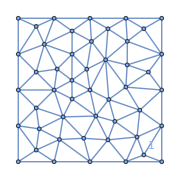
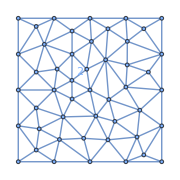
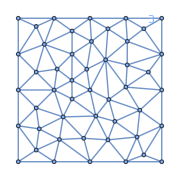

```mathematica
c=RadarCoordinates[g,b];
With[{d=Length[First[Values[c]]]},Row@Table[With[{levelSets=KeySort[GroupBy[Keys[c],c[#][[i]]&]],baseHue=(i-1)/d},With[{n=Length[levelSets]},HighlightGraph[g,Append[MapIndexed[Style[Subgraph[g,#1[[2]]],Directive[Thick,Hue[baseHue,0.9,0.3+0.6*(#2[[1]]-1)/Max[n-1,1]]]]&,Normal[levelSets]],Style[Labeled[b[[i]],i],Directive[Black,PointSize[Large]]]],ImageSize->Small]]],{i,d}]]
```

## Orthogonal Coordinates

Orthogonal coordinates of a vertex are the list of its shortest‑path projections onto a chosen set of lines, each line being parametrized by distance from a common center; these coordinates are most meaningful when the lines form an orthogonal frame, meaning each line has zero shortest‑path projection onto the others. There is a default tie-breaker that prefers 0 if it lies in the tied multi-coordinate, and otherwise returns the rounded median.

Find all orthogonal frames centered at a vertex with axes of given length:

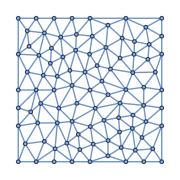
-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
g= MeshConnectivityGraph[ DiscretizeRegion[Rectangle[], MaxCellMeasure->.01] ];
c=FindInfraPoint[g,"From"->"Center"];
r=3;
f = FindInfraOrthogonalFrame[ g, c, r,All];
Row[InfraHighlightGraph[g,Join[ 
Thread[ #->(ColorData["Rainbow"]/@If[Length[#]==1,{0.5},Subdivide[0.1,0.9,Length[#]-1]]) ],
{c->Red,FindInfraShell[g,c,r]->Red}
],ImageSize->Small]&/@Take[f,5] ]
```

Find orthogonal coordinates with respect to the first orthogonal frame:

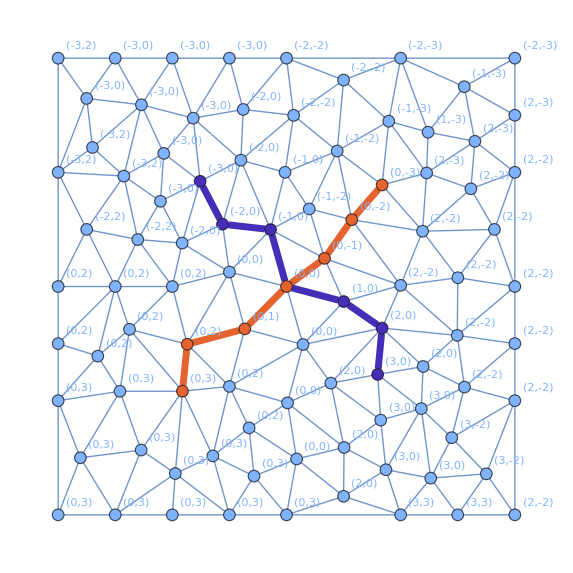

```mathematica
InfraHighlightGraph[Graph[g,VertexLabels-> KeyValueMap[#1->Row[{"(",#2[[1]],",",#2[[2]],")"}]&,OrthogonalCoordinates[g,c,#]]],Thread[ #->(ColorData["Rainbow"]/@Subdivide[0.1,0.9,Length[#]-1]) ]]& @f[[1]]
```

Visualize level sets of the orthogonal coordinates:

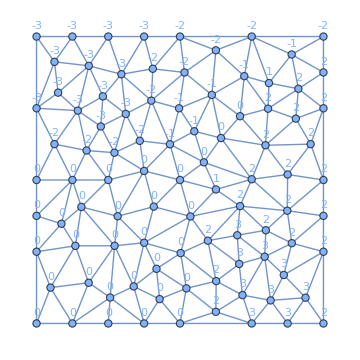
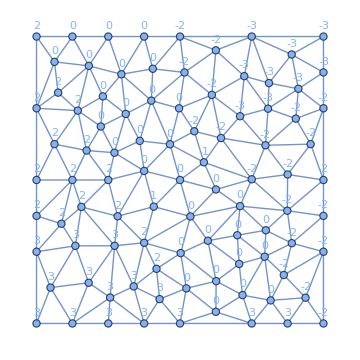

```mathematica
oc= OrthogonalCoordinates[g,c,f[[1]]];
With[{d=Length[f[[1]]]},Row@Table[With[{levelSets=KeySort[GroupBy[Keys[oc],oc[#][[i]]&]],baseHue=(i-1)/d},With[{n=Length[levelSets]},HighlightGraph[g,Append[MapIndexed[With[{t=(#2[[1]]-1)/Max[n-1,1]},Style[Subgraph[g,#1[[2]]],Directive[Thick,Hue[baseHue,1-0.7 t,0.2+0.75 t]]]]&,Normal[levelSets]],Style[Labeled[c,i],Directive[Black,PointSize[Large]]]],VertexLabels->KeyValueMap[#1->Placed[#2[[i]],Above]&,oc],ImageSize->Medium]]],{i,d}]]
```

Find orthogonal frames as the radius increases:

```mathematica
g=MeshConnectivityGraph[DiscretizeRegion[Rectangle[],MaxCellMeasure->.01]];
c=FindInfraPoint[g,"From"->"Center"];
maxR = 4;
Row[Table[With[{f=FindInfraOrthogonalFrame[g,c,r,1]},InfraHighlightGraph[g,Join[Thread[f[[1]]->(ColorData["Rainbow"]/@If[Length[f[[1]]]==1,{0.5},Subdivide[0.1,0.9,Length[f[[1]]]-1]])],{c->Red,FindInfraShell[g,c,r]->Red}],ImageSize->Small]],{r,Range[maxR]}]]
```

-Graphics--Graphics--Graphics--Graphics-

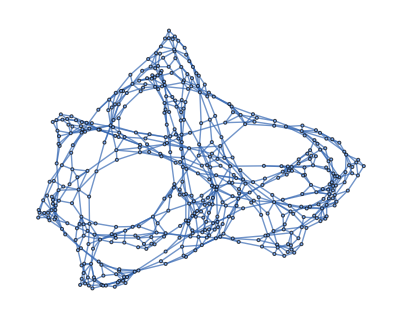

```mathematica
g = Graph[UndirectedEdge @@@ ResourceFunction["WolframModel"][{{x,y},{x,z}}->{{x,z},{x,w},{y,w},{z,w}},{{0,0},{0,0}},10,"FinalState"]]
```

```mathematica
c = FindInfraPoint[g,"From"->"Center"]
```

InfraPoint[{125}]

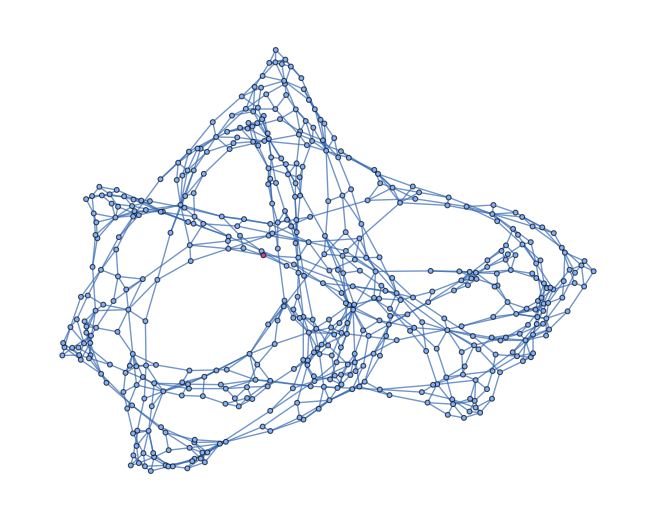

```mathematica
InfraHighlightGraph[g,{c}]
```

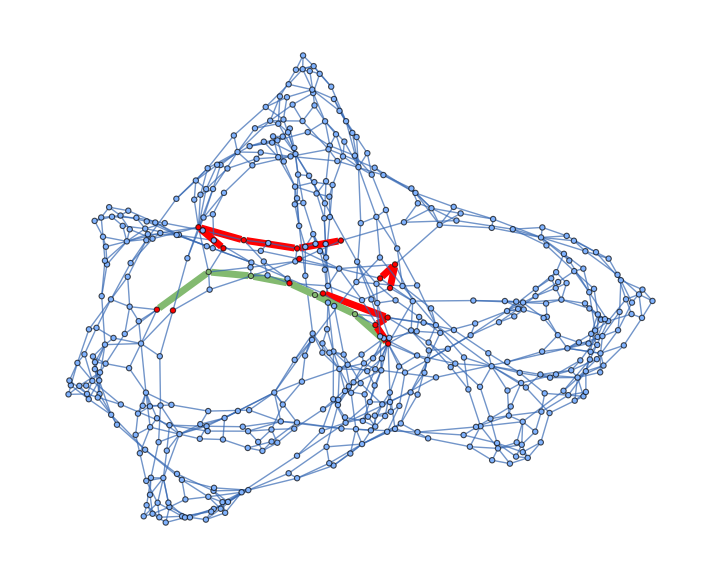
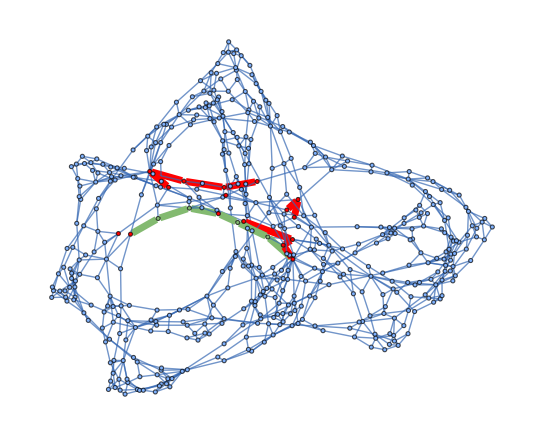
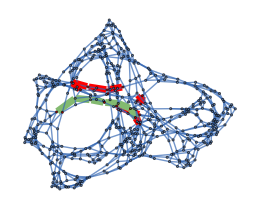
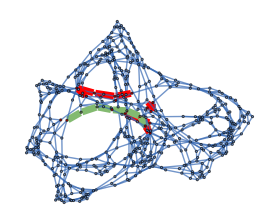
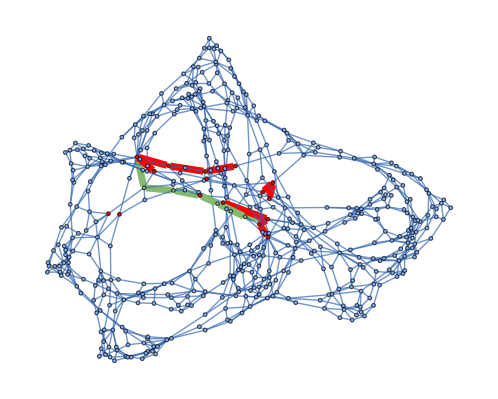

```mathematica
r=3;
f = FindInfraOrthogonalFrame[ g, c, r,All];
Row[InfraHighlightGraph[g,Join[ 
Thread[ #->(ColorData["Rainbow"]/@If[Length[#]==1,{0.5},Subdivide[0.1,0.9,Length[#]-1]]) ],
{c->Red,FindInfraShell[g,c,r]->Red}
],ImageSize->Small]&/@Take[f,5] ]
```

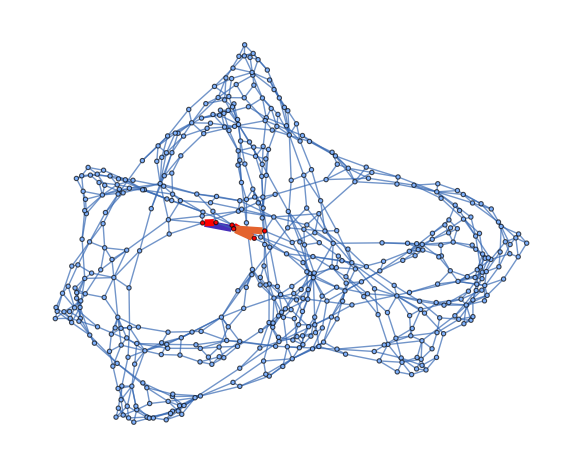
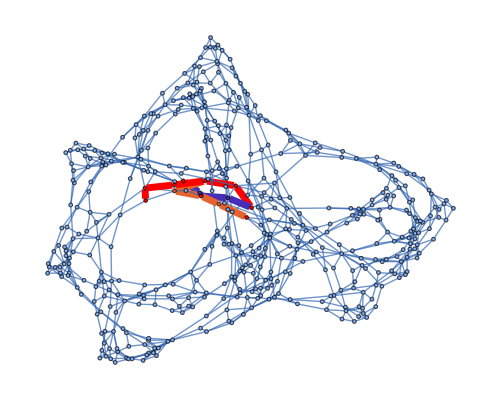
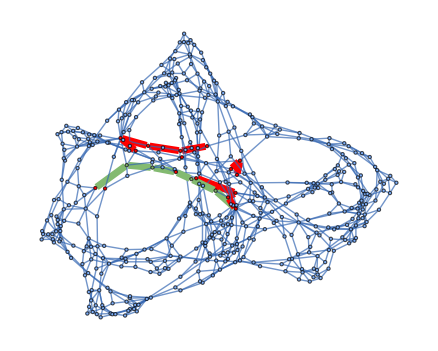
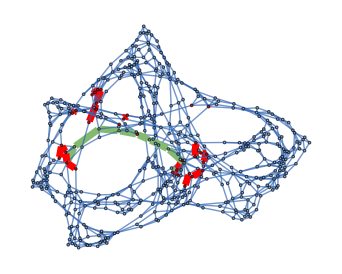

```mathematica
maxR = 4;
Row[Table[With[{f=FindInfraOrthogonalFrame[g,c,r,1]},InfraHighlightGraph[g,Join[Thread[f[[1]]->(ColorData["Rainbow"]/@If[Length[f[[1]]]==1,{0.5},Subdivide[0.1,0.9,Length[f[[1]]]-1]])],{c->Red,FindInfraShell[g,c,r]->Red}],ImageSize->Small]],{r,Range[maxR]}]]
```

## Orthogonal Coordinates

Orthogonal coordinates of a vertex are the list of its shortest‑path projections onto a chosen set of lines, each line being parametrized by distance from a common center; these coordinates are most meaningful when the lines form an orthogonal frame, meaning each line has zero shortest‑path projection onto the others. There is a default tie-breaker that prefers 0 if it lies in the tied multi-coordinate, and otherwise returns the rounded median.

Find all orthogonal frames centered at a vertex with axes of given length:

```mathematica
g= MeshConnectivityGraph[ DiscretizeRegion[Rectangle[], MaxCellMeasure->.01] ];
c=FindInfraPoint[g,"From"->"Center"];
r=3;
f = FindInfraOrthogonalFrame[ g, c, r,All];
Row[InfraHighlightGraph[g,Join[ 
Thread[ #->(ColorData["Rainbow"]/@If[Length[#]==1,{0.5},Subdivide[0.1,0.9,Length[#]-1]]) ],
{c->Red,FindInfraShell[g,c,r]->Red}
],ImageSize->Small]&/@Take[f,5] ]
```

-Graphics--Graphics--Graphics--Graphics--Graphics-

Find orthogonal coordinates with respect to the first orthogonal frame:

```mathematica
InfraHighlightGraph[Graph[g,VertexLabels-> KeyValueMap[#1->Row[{"(",#2[[1]],",",#2[[2]],")"}]&,OrthogonalCoordinates[g,c,#]]],Thread[ #->(ColorData["Rainbow"]/@Subdivide[0.1,0.9,Length[#]-1]) ]]& @f[[1]]
```

-Graphics-

Visualize level sets of the orthogonal coordinates:

```mathematica
oc= OrthogonalCoordinates[g,c,f[[1]]];
With[{d=Length[f[[1]]]},Row@Table[With[{levelSets=KeySort[GroupBy[Keys[oc],oc[#][[i]]&]],baseHue=(i-1)/d},With[{n=Length[levelSets]},HighlightGraph[g,Append[MapIndexed[With[{t=(#2[[1]]-1)/Max[n-1,1]},Style[Subgraph[g,#1[[2]]],Directive[Thick,Hue[baseHue,1-0.7 t,0.2+0.75 t]]]]&,Normal[levelSets]],Style[Labeled[c,i],Directive[Black,PointSize[Large]]]],VertexLabels->KeyValueMap[#1->Placed[#2[[i]],Above]&,oc],ImageSize->Medium]]],{i,d}]]
```

-Graphics--Graphics-

Find orthogonal frames as the radius increases:

```mathematica
g=MeshConnectivityGraph[DiscretizeRegion[Rectangle[],MaxCellMeasure->.01]];
c=FindInfraPoint[g,"From"->"Center"];
maxR = 4;
Row[Table[With[{f=FindInfraOrthogonalFrame[g,c,r,1]},InfraHighlightGraph[g,Join[Thread[f[[1]]->(ColorData["Rainbow"]/@If[Length[f[[1]]]==1,{0.5},Subdivide[0.1,0.9,Length[f[[1]]]-1]])],{c->Red,FindInfraShell[g,c,r]->Red}],ImageSize->Small]],{r,Range[maxR]}]]
```

-Graphics--Graphics--Graphics--Graphics-

```mathematica
g = Graph[UndirectedEdge @@@ ResourceFunction["WolframModel"][{{x,y},{x,z}}->{{x,z},{x,w},{y,w},{z,w}},{{0,0},{0,0}},10,"FinalState"]]
```

-Graphics-

```mathematica
c = FindInfraPoint[g,"From"->"Center"]
```

InfraPoint[{125}]

```mathematica
InfraHighlightGraph[g,{c}]
```

-Graphics-

```mathematica
r=3;
f = FindInfraOrthogonalFrame[ g, c, r,All];
Row[InfraHighlightGraph[g,Join[ 
Thread[ #->(ColorData["Rainbow"]/@If[Length[#]==1,{0.5},Subdivide[0.1,0.9,Length[#]-1]]) ],
{c->Red,FindInfraShell[g,c,r]->Red}
],ImageSize->Small]&/@Take[f,5] ]
```

-Graphics--Graphics--Graphics--Graphics--Graphics-

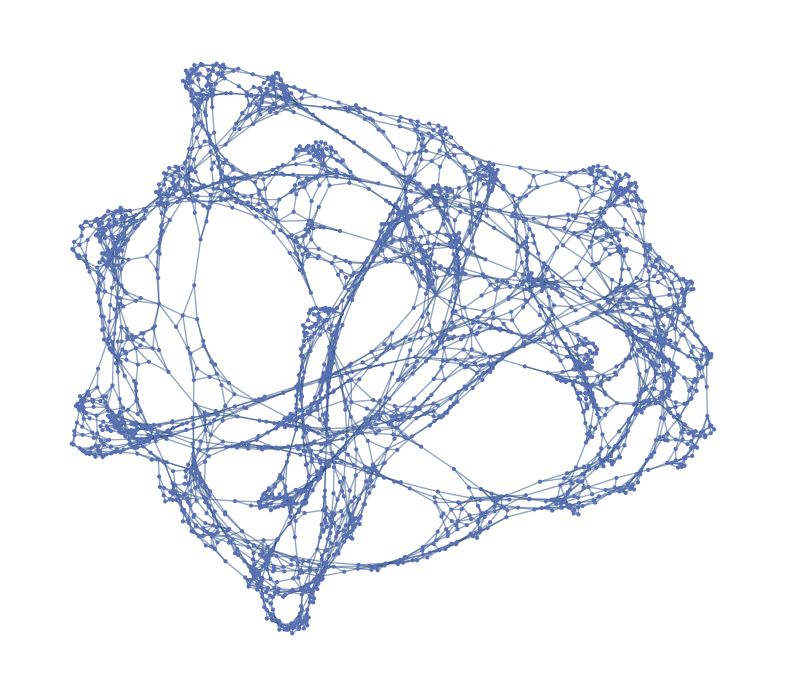

```mathematica
g = Graph[UndirectedEdge @@@ ResourceFunction["WolframModel"][{{x,y},{x,z}}->{{x,z},{x,w},{y,w},{z,w}},{{0,0},{0,0}},13,"FinalState"]]
```

```mathematica
c = FindInfraPoint[g,"From"->"Center"]
```

InfraPoint[{2}]

```mathematica
maxR = 2;
Row[Table[With[{f=FindInfraOrthogonalFrame[g,c,r,1]},InfraHighlightGraph[g,Join[Thread[f[[1]]->(ColorData["Rainbow"]/@If[Length[f[[1]]]==1,{0.5},Subdivide[0.1,0.9,Length[f[[1]]]-1]])],{c->Red,FindInfraShell[g,c,r]->Red}],ImageSize->Small]],{r,Range[maxR]}]]
```

$Aborted

```mathematica
r=2;
f = FindInfraOrthogonalFrame[ g, c, r,All];
Row[InfraHighlightGraph[g,Join[ 
Thread[ #->(ColorData["Rainbow"]/@If[Length[#]==1,{0.5},Subdivide[0.1,0.9,Length[#]-1]]) ],
{c->Red,FindInfraShell[g,c,r]->Red}
],ImageSize->Small]&/@Take[f,5] ]
```

-Graphics--Graphics--Graphics--Graphics--Graphics-

Action items:

10 graphs that we can use as examples

Make sure the algorithm is local